```mathematica
(*With Damage*)
```

```mathematica
x'[t]=g*x[t]*(1-x[t]/a)-h[t];
prof[t]=(150-17.21*h[t])*h[t]+R*(1-c*x[t]);
```

```mathematica
(*H & MP*)
```

```mathematica
Ham=prof[t]+μ[t]*x'[t]
dHdh=D[Ham,h[t]]
μ'[t]=FullSimplify[r*μ[t]-D[Ham,x[t]]]
```

(150-17.21 h[t]) h[t]+R (1-c x[t])+(-h[t]+g x[t] (1-x[t]/a)) μ[t]

150-34.42 h[t]-μ[t]

c R+(-g+r+(2 g x[t])/a) μ[t]

```mathematica
μ1[t]=μ[t]/.Solve[dHdh==0,μ[t]][[1]]
μ1dot=FullSimplify[D[μ1[t],t]]
```

-1. (-150.+34.42 h[t])

-34.42 h'[t]

```mathematica
Δμ1dot = Simplify[(μ1dot-μ'[t])/.μ[t]-> μ1[t]]
Variables[Δμ1dot]
```

-c R+1. (-150.+34.42 h[t]) (-g+r+(2 g x[t])/a)-34.42 h'[t]

{c,R,h[t],g,r,a,x[t],h'[t]}

```mathematica
h'[t]=h'[t]/.Solve[Δμ1dot ==0,h'[t]][[1]]
```

-0.0290529 (1. c R-1. (-150.+34.42 h[t]) (-1. g+r+(2. g x[t])/a))

```mathematica
(*Isoclines*)
```

```mathematica
hiso=x[t]/.Solve[h'[t]==0,x[t]][[1]]
xiso=h[t]/.Solve[x'[t]==0,h[t]][[1]]
```

(17.21 a (0.0290529 c R+0.0290529 g (-150.+34.42 h[t])-0.0290529 r (-150.+34.42 h[t])))/(g (-150.+34.42 h[t]))

-(g x[t] (-a+x[t]))/a

```mathematica
Solve[hiso-xiso==0,x[t]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x[t]→(0.5 a (g-1. √(g^2-(300. g)/(150.-34.42 h[t])+(300. r)/(150.-34.42 h[t])+(2. c R)/(150.-34.42 h[t])+(68.84 g h[t])/(150.-34.42 h[t])-(68.84 r h[t])/(150.-34.42 h[t]))))/g},{x[t]→(0.5 a (g+√(g^2-(300. g)/(150.-34.42 h[t])+(300. r)/(150.-34.42 h[t])+(2. c R)/(150.-34.42 h[t])+(68.84 g h[t])/(150.-34.42 h[t])-(68.84 r h[t])/(150.-34.42 h[t]))))/g}}

```mathematica
(*Data*)
```

```mathematica
g=.5840;
hmax=g*(7.5)*(1-.5)
r=0.1;
a=15;
R = 100;
c = 0.06;
```

2.19

```mathematica
Solve[hiso-xiso==0,x[t]]
FullSimplify[Solve[{x'[t]==0, h'[t]==0},{x[t],h[t]}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x[t]→0.10274 (73.-(2. √(1.60238×10^7-4.21473×10^6 h[t]))/(√(-7500.+1721. h[t])))},{x[t]→0.10274 (73.+(2. √(1.60238×10^7-4.21473×10^6 h[t]))/(√(-7500.+1721. h[t])))}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x[t]→5.26793,h[t]→1.99603},{x[t]→7.97391-7.58777 ⅈ,h[t]→4.42281+0.280003 ⅈ},{x[t]→7.97391+7.58777 ⅈ,h[t]→4.42281-0.280003 ⅈ}}

```mathematica
(*Isoclines*)
```

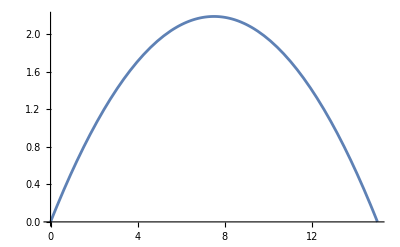

```mathematica
Plot[{xiso,hiso},{x[t],0,15}]
```

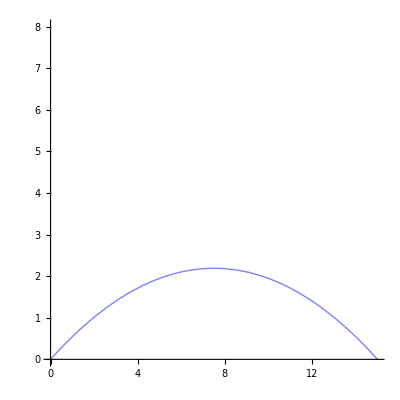

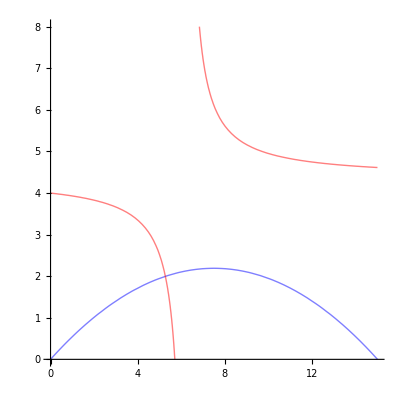

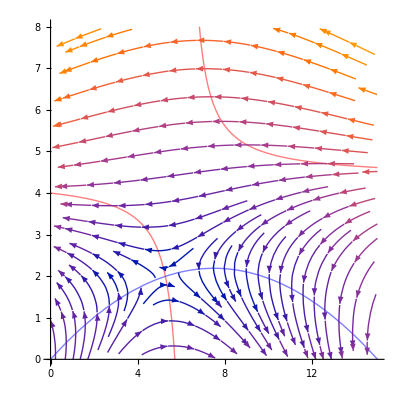

```mathematica
xdot=ContourPlot[x'[t],{x[t],0,15},{h[t],0,8},Frame->False,Axes->True,ContourShading->False,  Contours->{0},ContourStyle->{Blue}]
hdot=ContourPlot[h'[t],{x[t],0,15},{h[t],0,8},Frame->False,Axes->True,ContourShading->False,  PlotPoints->25,Contours->{0},ContourStyle->{Red}];
p3 = StreamPlot[{x'[t],h'[t]},{x[t],0,15},{h[t],0,8}];
Show[xdot,hdot]
Show[xdot,hdot,p3]
```

```mathematica
(*Steady State*)
```

```mathematica
FullSimplify[Solve[{x'[t]==0, h'[t]==0},{x[t],h[t]}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x[t]→5.26793,h[t]→1.99603},{x[t]→7.97391-7.58777 ⅈ,h[t]→4.42281+0.280003 ⅈ},{x[t]→7.97391+7.58777 ⅈ,h[t]→4.42281-0.280003 ⅈ}}

```mathematica
Clear[x1,y1,x2,h2,h3,h3]
eq1=x'[t]==0;
eq2=h'[t]==0;
{x1,h1}={x[t],h[t]}/.FindRoot[{eq1,eq2},{x[t],0},{h[t],0}]
{x2,h2}={x[t],h[t]}/.FindRoot[{eq1,eq2},{x[t],7},{h[t],3}]
{x3,h3}={x[t],h[t]}/.FindRoot[{eq1,eq2},{x[t],10},{h[t],5}]
"             Steady State Pairs"
{x1,h1}
{x2,h2}
{x3,h3}
```

{5.26793,1.99603}

{5.26793,1.99603}

{5.26793,1.99603}

Steady State Pairs

{5.26793,1.99603}

{5.26793,1.99603}

{5.26793,1.99603}

```mathematica
(*Eigenvalues*)
```

```mathematica
dotx=x'[t]/.{x[t]->xa,h[t]->ha};
doth=h'[t]/.{x[t]->xa,h[t]->ha};
```

```mathematica
xdotx=D[dotx, xa];
xdoth=D[dotx, ha];
hdotx=D[doth, xa];
hdoth=D[doth, ha];
```

```mathematica
j:={{xdotx,xdoth},{hdotx,hdoth}}
FullSimplify[Eigenvalues[j]]
```

{0.05-0.5 √(2.49797-0.311467 ha+(-0.332646+0.0242529 xa) xa),0.5 (0.1+√(2.49797-0.311467 ha+(-0.332646+0.0242529 xa) xa))}

```mathematica
j:={{xdotx,xdoth},{hdotx,hdoth}}
eig[xa_,ha_]=Eigenvalues[j]
"        Eigenvalues for the different Steady States"
eig[x1,h1]
eig[x2,h2]
eig[x3,h3]
```

{1/2 (0.1-√(2.49797-0.311467 ha-0.332646 xa+0.0242529 xa^2)),1/2 (0.1+√(2.49797-0.311467 ha-0.332646 xa+0.0242529 xa^2))}

Eigenvalues for the different Steady States

{-0.396364,0.496364}

{-0.396364,0.496364}

{-0.396364,0.496364}

```mathematica
(*Paths*)
```

```mathematica
xx'[t]=x'[t]/.{x[t]->xb[t],h[t]->hb[t]};
hh'[t]=h'[t]/.{x[t]->xb[t],h[t]->hb[t]};
```

```mathematica
xbdot=ContourPlot[xx'[t],{xb[t],0,15},{hb[t],0,8},Frame->False,Axes->True,ContourShading->False,  Contours->{0},ContourStyle->{Blue}]
hbdot=ContourPlot[hh'[t],{xb[t],0,15},{hb[t],0,8},Frame->False,Axes->True,ContourShading->False,  PlotPoints->25,Contours->{0},ContourStyle->{Red}];
pb3 = StreamPlot[{xx'[t],hh'[t]},{xb[t],0,15},{hb[t],0,8}];
Show[xbdot,hbdot]
Show[xbdot,hbdot,pb3]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
t1=-25.1019;
t2=-25.1019;
```

```mathematica
ode1[xb0_,hb0_]:=NDSolve[{xb'[t]==xx'[t],hb'[t]==hh'[t],xb[0]==xb0,hb[0]==hb0},{xb[t],hb[t]},{t,t1,0}];
ode2[xb02_,hb02_]:=NDSolve[{xb'[t]==xx'[t],hb'[t]==hh'[t],xb[0]==xb02,hb[0]==hb02},{xb[t],hb[t]},{t,t2,0}];
```

```mathematica
sol[1]=ode1[x2-.0005,h2-.0005] ;
sol2[1]=ode2[x2+.0005,h2+.0005] ;
```

```mathematica
plt=ParametricPlot[Evaluate[Table[{xb[t],hb[t]}/.sol[1]]],{t,0,t1}, PlotRange->{{0,15},{0,8}},PlotPoints->100,AxesLabel->{"x","h"},AspectRatio ->.5,PlotStyle->Directive[Red,Thick]];
plt2=ParametricPlot[Evaluate[Table[{xb[t],hb[t]}/.sol2[1]]],{t,0,t2}, PlotRange->{{0,15},{0,8}},PlotPoints->100,AxesLabel->{"x","h"},AspectRatio ->.5,PlotStyle->Directive[Red,Thick]];
```

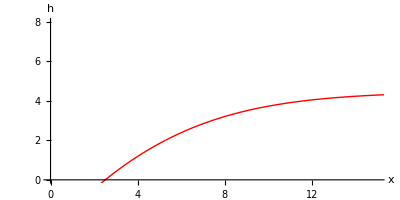

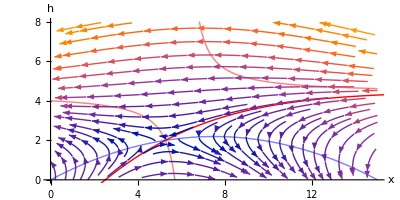

```mathematica
Show[{plt,plt2},PlotRange->{{0,15},{0,8}},AxesLabel->{"x","h"}]
Show[plt,plt2,xbdot,hbdot,pb3]
```

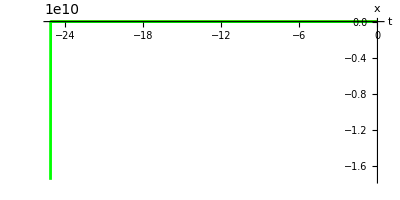

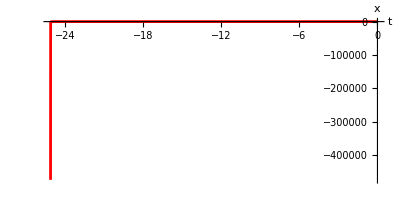

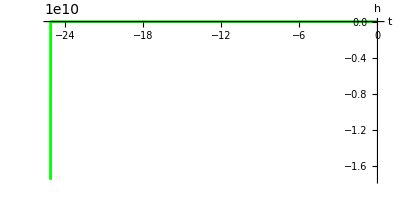

```mathematica
"Time Paths";
pltxb=ParametricPlot[Evaluate[{t,xb[t]}/. sol[1]],{t,0,t1},PlotRange->{{0,t1},{0,15}},AxesLabel->{"t","x"},AxesOrigin->{0,0},AspectRatio->.5,PlotStyle->{Red}];
plthb=ParametricPlot[Evaluate[{t,hb[t]}/. sol[1]],{t,0,t1},PlotRange->{{0,t1},{0,8}},AxesLabel->{"t","h"},AxesOrigin->{0,0},AspectRatio->.5,PlotStyle->{Green}];
Show[pltxb,plthb,Method->{"AxesInFront"->False}]
Show[pltxb,Method->{"AxesInFront"->False}]
Show[plthb,Method->{"AxesInFront"->False}]
```